100

{176.,293.,385.5,389.5,390.5}

(0.+176. q^2 | 100. | 0. | 0. | 0.
100. | 206.576+293. (-0.41+q)^2 | 100. | 0. | 0.
0. | 100. | 635.549+385.5 (-0.82+q)^2 | 100. | 0.
0. | 0. | 100. | 1303.34+389.5 (-1.23+q)^2 | 100.
0. | 0. | 0. | 100. | 2294.94+390.5 (-1.64+q)^2)

Root::deg: PiecewiseDump`X$62286[1] has fewer than 2 root(s) as a polynomial in PiecewiseDump`X$62286[1].

Root::deg: PiecewiseDump`X$62286[1] has fewer than 3 root(s) as a polynomial in PiecewiseDump`X$62286[1].

Root::deg: PiecewiseDump`X$62286[1] has fewer than 4 root(s) as a polynomial in PiecewiseDump`X$62286[1].

General::stop: Further output of Root::deg will be suppressed during this calculation.

342.797

-36.7721

0.0817375

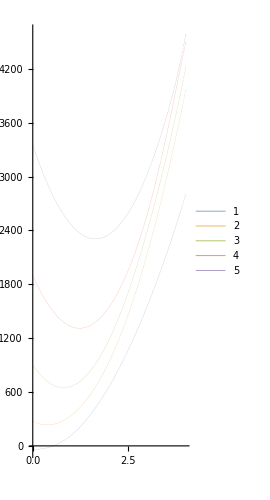

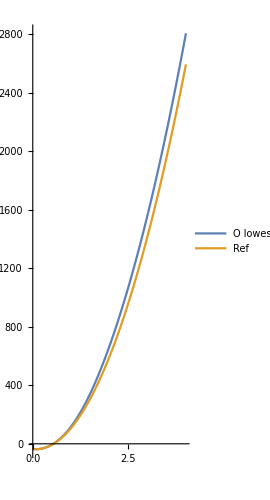

```mathematica
(*The energy landscape*)
ClearAll["Global`*"]
eneQ[q_,q0_]:=(q-q0)^2;
eneK[k_]:=0.5*k
Q0={0,0.41,0.82,1.23,1.64};
V={0,206.576,635.549,1303.336,2294.939};
K0={352,586,771,779,781};
K1=(10/4)^2*{352,838,1871,1986,2117};
c=100

selfQ=eneQ[q,#]&/@Q0;
selfK=eneK[#]&/@K0
EneMat=DiagonalMatrix[selfQ]* DiagonalMatrix[selfK];
overlap={c,c,c,c};
Overlap1=DiagonalMatrix[overlap,1];
Overlap2=DiagonalMatrix[overlap,-1];
Vmat=DiagonalMatrix[V];
EneMatFinal=EneMat+Overlap1+Overlap2+Vmat;
EneMatFinal//MatrixForm
values=Eigenvalues[EneMatFinal];
lowest = Min[values];


minima=FindMinimum[lowest,q];
APt=D[D[lowest,q],q]/.minima[[2]]
CPt=minima[[1]]
q0Pt=q/.minima[[2]]
Plot[{values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]},{q,0,4},PlotRange->Full,AspectRatio->Full,PlotLegends->{"1","2","3","4","5"},PlotStyle->Thickness[0]]
Plot[{lowest,0.5*APt*(q-q0Pt)^2+CPt},{q,0,4},PlotRange->Full,AspectRatio->Full,PlotLegends->{"O lowest","Ref"}]
```

(422. q^2 | 1. | 0.
1. | -141+265. (0.41+q)^2 | 1.
0. | 1. | 603+334.5 (0.82+q)^2)

Root::deg: PiecewiseDump`X$62639[1] has fewer than 2 root(s) as a polynomial in PiecewiseDump`X$62639[1].

Root::deg: PiecewiseDump`X$62639[1] has fewer than 3 root(s) as a polynomial in PiecewiseDump`X$62639[1].

Root::deg: PiecewiseDump`X$62639[1] has fewer than 2 root(s) as a polynomial in PiecewiseDump`X$62639[1].

General::stop: Further output of Root::deg will be suppressed during this calculation.

529.982

-141.006

-0.409986

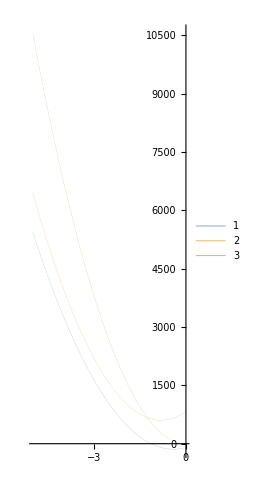

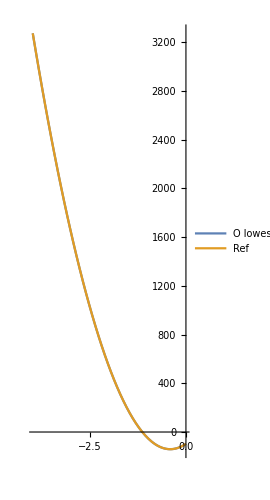

```mathematica
QO={0,-.41,-.82};
VO={0,-141,603};
KO={844,530,669};
cO=1;
selfQO=eneQ[q,#]&/@QO;
selfKO=eneK[#]&/@KO;
EneMatO=DiagonalMatrix[selfQO]*DiagonalMatrix[selfKO];
overlapO={cO,cO};
Overlap1O=DiagonalMatrix[overlapO,1];
Overlap2O=DiagonalMatrix[overlapO,-1];
VmatO=DiagonalMatrix[VO];
EneMatFinalO=EneMatO+Overlap1O+Overlap2O+VmatO;
EneMatFinalO//MatrixForm
valuesO=Eigenvalues[EneMatFinalO];
lowestO= Min[valuesO];
minimaO=FindMinimum[lowestO,q];
AO=D[D[lowestO,q],q]/.minimaO[[2]]
CO=minimaO[[1]]
q0O=q/.minimaO[[2]]

Plot[{valuesO[[1]],valuesO[[2]],valuesO[[3]]},{q,0,-5},PlotRange->Full,AspectRatio->Full,PlotLegends->{"1","2","3","4","5"},PlotStyle->Thickness[0]]
Plot[{lowestO,0.5*AO*(q-q0O)^2+CO},{q,-4,0},PlotRange->Full,AspectRatio->Full,PlotLegends->{"O lowest","Ref"}]
```